## Newton — Problem Set 4 — Solution

### 1. A Very Strange Central Force Law

This is actually quite relevant to understanding Proposition 7. Both are about the strange forces that are needed to keep an object going around an off-center figure, but also that such contrived forces can be constructed.

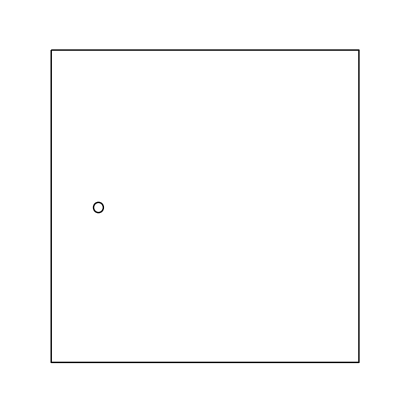

A planet orbits counterclockwise in a square about a star, but the star is offset to the left from the center of the square, as shown above. If the square has sides of length 2a, and the offset from the center to the left is e, then the planet comes as close as a-e to the star when it is traveling down the left side of the square. Its closest approach to the star as it travels right across the bottom is simply a. As it goes up the right side of the square, its closest approach is a+e. When it is traveling left across the top its closest approach is again just a.

If it travels at constant speed v_leftwhen going down the left side, and constant speed v_across on both the bottom and top sides, and constant speed v_right going up the right side, then the planet is moving uniformly and freely along those sides.

(a) The main job of this problem is to figure out what must happen at the corners. There is definitely a change in the quantity of motion at the corners. The cool thing is that if the change in the quantity of motion is due to a centripetal force, then this sets up relationships among v_left, v_across, and v_right. In other words, if you know one, say v_left, then you can determine the other two in terms of v_left. Your formulas will involve a and e.

There are two ways of doing this problem that correspond to using Proposition 1 or not using Proposition 1. Do it using the equal areas in equal times law for centripetal forces (in other words, do it using the result of Proposition 1).

(b) You now have a relationship between v_left and v_across. Using this relationship compute the direction of the impressed force (that effected the change of motion in the lower-left corner). It will be another formula involving a and e. Does it point toward the star? It better! If it doesn’t re-check your work in both the previous part and this part. (Note: The mass of the planet is an unspecified unknown which is part of the quantity of motion. However, you don’t need to know it to find the direction asked for.)

(c) You have formulas for v_right and v_across. There is a change in the quantity of motion at the lower-right hand corner which can be expressed in terms of v_left, a, and e. What is the ratio of the change in quantity of motion at this corner to the change in the quantity of motion at the lower-left corner? One expects v_left to disappear from the ratio, leaving a formula only involving a and e.

### 2. Radii of Curvature — Newton’s Construction Involving Chords

(a) First, let’s apply Newton’s construction to the circle. This is especially important since Newton appeals directly to the properties of the circle when he is trying to understand the curvature of an arc.

The equation for a circle of radius 1 is y =-√(1-x^2)+1. I added the +1 so that the circle would pass through the origin. Also, this is only the equation for lower half of the circle. The rest of it you would get from y=√(1-x^2)+1, but we don’t need the upper half.

You are going to find out where the perpendiculars to the chords meet. Accurately draw chords starting at the origin (x=y=0), and going to points on the circle. The slopes of these chords are given by the rise over run. Since I arranged for one end of the chord to be at (0, 0) this is just y over x, or (-√(1-x^2)+1)/x. The slope of the perpendicular to the tangent is minus the reciprocal of this, so it is -x/(-√(1-x^2)+1). You now have more than enough information to create a table and then draw in the chords and their perpendiculars focusing on the region between x=-0.3 and 0.3. Where do those perpendiculars intersect the y-axis? Below is a place to plot your results.

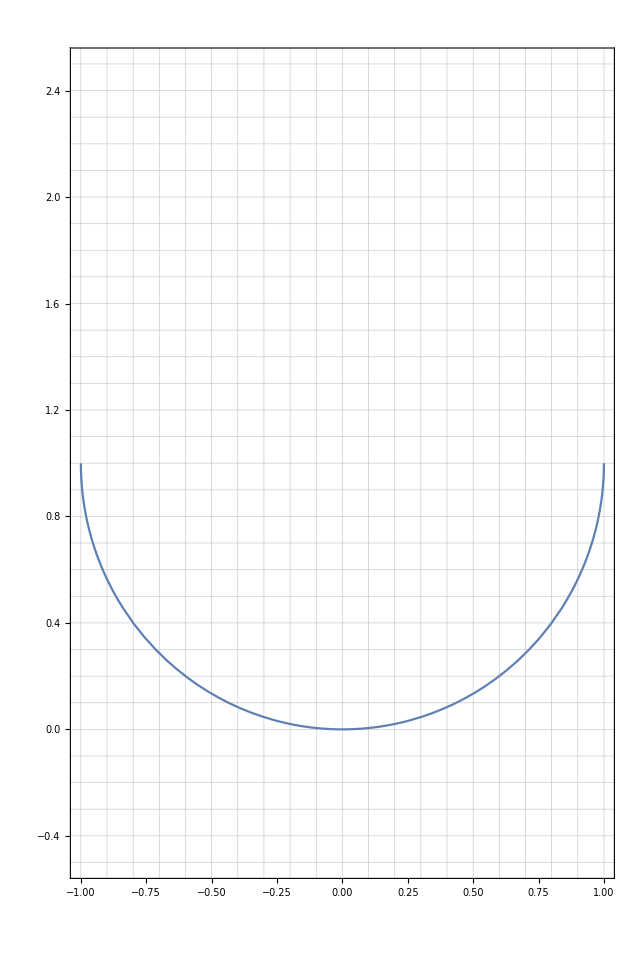

```mathematica
Plot[-Sqrt[1-x^2]+1, {x, -1, 1}, PlotRange->{{-1, 1}, {-0.5, 2.5}}, AspectRatio->3/2, GridLines->{Range[-1, 1, 0.1], Range[-0.5, 2.5, 0.1]}, Frame->True]
```

(b) Next a very tricky situation for Newton: a curve around a point with no curvature. Consider the curve defined by y=5 x^4. It has no curvature at x=0.

Accurately draw chords to the curve with one end at the origin and the other end along the curve and perpendiculars to those chords in the region focusing especially on the region between x=-0.5 and 0.5. Just as in Part (a), the slope of the chords is given by y/x, which for this function simplifies to 5 x^3. The slope of the perpendiculars is minus the reciprocal of this, so that is -1/(5 x^3).

Where do those perpendiculars intersect the y-axis? Is this converging to anything as x the chords get shorter and shorter? Below is a place to plot your results.

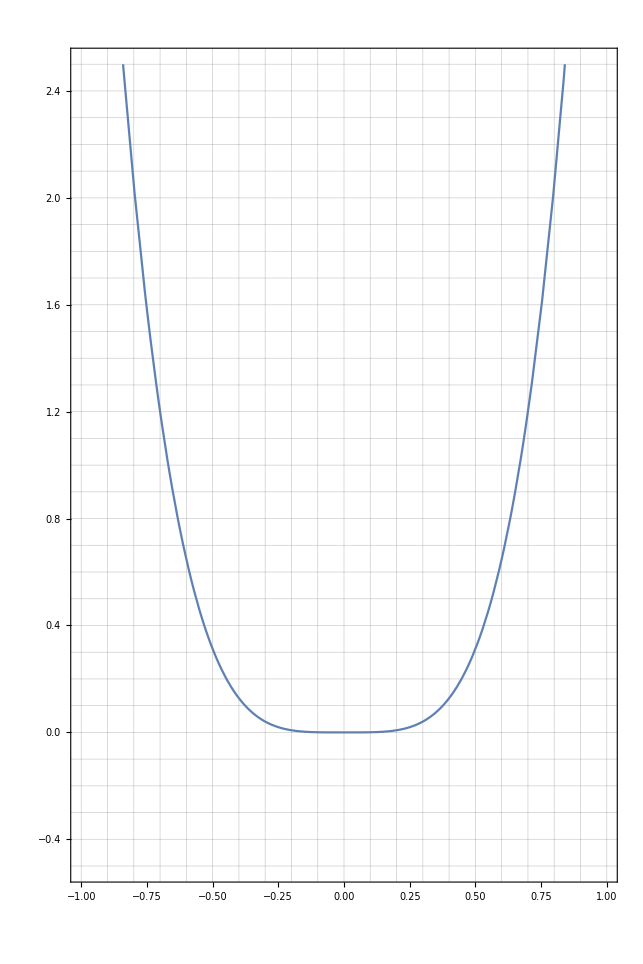

```mathematica
Plot[5 x^4, {x, -1, 1}, PlotRange->{{-1, 1}, {-0.5, 2.5}}, AspectRatio->3/2, GridLines->{Range[-1, 1, 0.1], Range[-0.5, 2.5, 0.1]}, Frame->True]
```

(c) Finally, a more normal situation using another function: y=x^3+x^2. This time we have some curvature at y=x=0.

Accurately draw the chords to this curve and perpendiculars to those chords, focusing especially on the region between x=-0.3 and 0.3. Where do those perpendiculars intersect the y-axis?

To do this accurately, you will need that the slope of the chord to this function is y/x=(x^3+x^2)/x=x^2+x. Therefore the slope of the perpendiculars is -1/(x^2+x). Proceed as in (a) and (b).

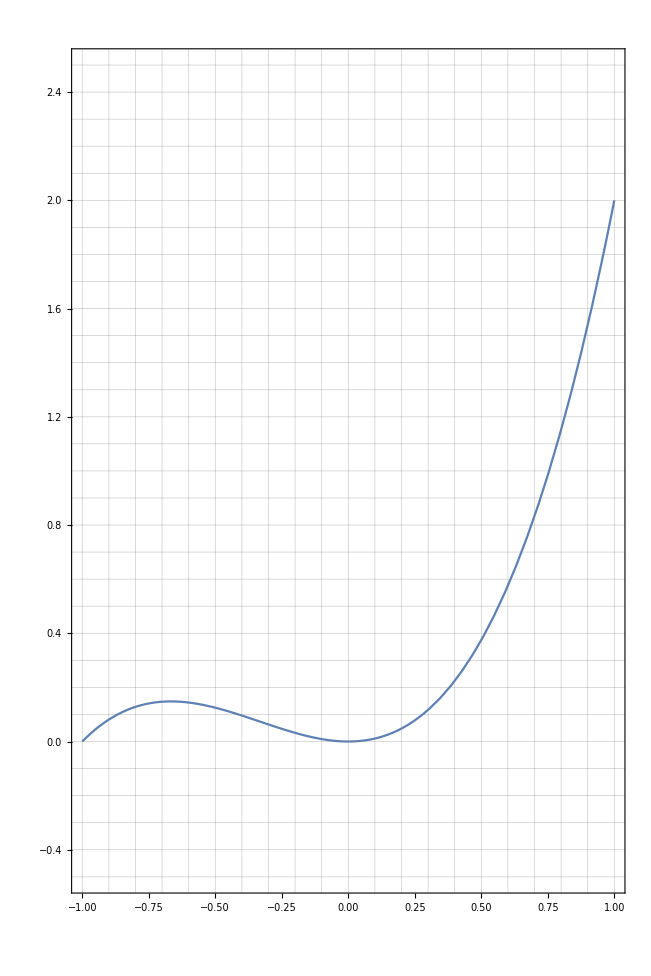

```mathematica
Plot[x^3+x^2, {x, -1, 1}, PlotRange->{{-1, 1}, {-0.5, 2.5}}, AspectRatio->3/2, GridLines->{Range[-1, 1, 0.1], Range[-0.5, 2.5, 0.1]}, Frame->True]
```

### 3. Period Associated with the Van Der Waals Force

The Van Der Waals attraction between neutral spherically-symmetric atoms (wait, there is an attraction between neutral, spherically-symmetric atoms!?) is modeled as a centripetal force of size F_r, where F_r is minus the derivative of ϵ((σ/r)^12-2(σ/r)^6) with respect to r. If you didn’t understand that, no problem. You just need to know that the force is 12ϵ((σ/r)^13-(σ/r)^7)/σ. This radial force is repulsive for r<σ so there are no orbits there. However, it is attractive (negative) for r>σ. Is it possible to write an equation that would tell you the relationship between the period and the radius, as Newton did for many simpler force laws which he summarized in Proposition 4, Corollary 7?

You don’t know the mass of the atom, and that must enter in somehow because the same Van Der Waals force cannot keep a heavier atom in the same orbit with the same period as it keeps a light atom in that orbit with that period.

If it helps you get something, go ahead and appeal to the modern version of F=ma applied to circular motion, F_r=-m v^2/r. Newton has not (quite) given us this! From Newton, we know only that F_r is proportional to v^2, that it is also proportional to m, and that it is also inversely proportional to r. If you can arrive at some result using only these things and not the modern algebraic equation that summarizes those things, show us all how!

### 4 and 5. Create Two Good Exam Problems

You can of course define “good” as you see fit, but my likely considerations would be: (a) The problem should demonstrate that you can apply the theory Newton is developing and/or use his methods as he does, (b) It should be instructive and/or illustrative to do the problem or see its results, and (c) It should be amenable to objective grading. Also, (d) It shouldn’t be too easy or too hard.